```mathematica
Es=Flatten[Import["/home/cjohns10/research/4BodySVD/eSpacings-150x80x80x200x40-m1234.dat"]];eTrim = Select[Es,#>0.0000001&];
Length[Es]
Length[eTrim]
```

89

89

```mathematica
bins=Table[x,{x,0,5,0.2}];
```

```mathematica
bFit=Table[0.5*(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}];
```

```mathematica
EspaceBin=BinCounts[eTrim,{bins}];
```

```mathematica
NormBrodyBinCs=Table[EspaceBin[[i]]/Total[EspaceBin]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}];
```

```mathematica
Remove[al,p]
```

```mathematica
alpha[q_]:=(Gamma[(q+2)/(q+1)])^(q+1)
```

```mathematica
p[q_,s_]:=alpha[q]*(q+1)*s^(q)*E^(-alpha[q]*s^(q+1))
```

```mathematica
brodyPdist = Table[{bFit[[i]],NormBrodyBinCs[[i]]},{i,1,Length[bFit]}]
```

{{0.1,0.168539},{0.3,0.617978},{0.5,1.01124},{0.7,0.505618},{0.9,0.730337},{1.1,0.505618},{1.3,0.561798},{1.5,0.0561798},{1.7,0.280899},{1.9,0.0561798},{2.1,0.168539},{2.3,0.11236},{2.5,0.},{2.7,0.0561798},{2.9,0.11236},{3.1,0.},{3.3,0.0561798},{3.5,0.},{3.7,0.},{3.9,0.},{4.1,0.},{4.3,0.},{4.5,0.},{4.7,0.},{4.9,0.}}

```mathematica
p1=ListPlot[brodyPdist,InterpolationOrder->0,Joined->True,PlotRange->All,PlotStyle->Red];
```

```mathematica
pars = FindFit[brodyPdist,{p[q,s],q>0,q<1},{q},s]
```

{q→0.644813}

```mathematica
p2=Plot[p[q/.pars,s],{s,0,5},PlotRange->All,PlotStyle->Red];
```

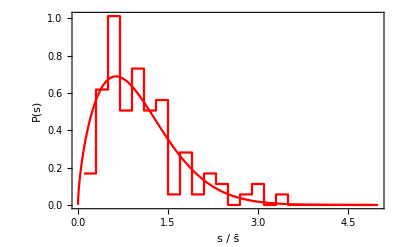

```mathematica
Show[p1,p2,PlotRange->All,FrameLabel->{"s / s̄","P(s)"},Frame-> True,LabelStyle->Large]
```